# Prueba de prácticas

## Asignatura: Fecha: Nombre: DNI: Grupo de prácticas: Modelo de examen: Grupo de teoría (A o B):

Ejercicio 1

```mathematica
prem1[{p_,q_,r_}]:=(p⇒(q∧r))
prem2[{p_,q_,r_}]:=((¬q)∨(¬r))
concl[{p_,q_,r_}]:= (¬p)
```

```mathematica
n=3;
FormaE[v_]:=(prem1[v] ∧prem2[v])⇒concl[v];
tautologia=True;
p=Table[False,{t,n}];
For[i=0,i<2^n,i++,
j=i;
For[f=n,f>0,f--,
resto=Mod[j,2];
j=Floor[j/2];
If[resto==0,p[[f]]=True,p[[f]]=False];
];
If[FormaE[p],Null,tautologia=False];
];
If[tautologia,Print["La forma enunciativa es una tautología"],Print["La forma enunciativa no es una tautología"]]
```

La forma enunciativa es una tautología

Como la forma enunciativa es una tautología entonces es una argumentación válida

## Ejercicio 2

```mathematica
Deje2=Divisors[72]
CARTESIANO[conjuntos_]:=Module[{i,j,k,cartesianotemp},cartesiano=Table[{conjuntos[[1,i]]},{i,Length[conjuntos[[1]]]}];
Do[cartesianotemp={};
Do[Do[AppendTo[cartesianotemp,Append[cartesiano[[k]],conjuntos[[i,j]]]];,{k,Length[cartesiano]}];,{j,Length[conjuntos[[i]]]}];
cartesiano=cartesianotemp;,{i,2,Length[conjuntos]}];
cartesiano];
```

{1,2,3,4,6,8,9,12,18,24,36,72}

```mathematica
cart = CARTESIANO[{Deje2,Deje2}]
```

{{1,1},{2,1},{3,1},{4,1},{6,1},{8,1},{9,1},{12,1},{18,1},{24,1},{36,1},{72,1},{1,2},{2,2},{3,2},{4,2},{6,2},{8,2},{9,2},{12,2},{18,2},{24,2},{36,2},{72,2},{1,3},{2,3},{3,3},{4,3},{6,3},{8,3},{9,3},{12,3},{18,3},{24,3},{36,3},{72,3},{1,4},{2,4},{3,4},{4,4},{6,4},{8,4},{9,4},{12,4},{18,4},{24,4},{36,4},{72,4},{1,6},{2,6},{3,6},{4,6},{6,6},{8,6},{9,6},{12,6},{18,6},{24,6},{36,6},{72,6},{1,8},{2,8},{3,8},{4,8},{6,8},{8,8},{9,8},{12,8},{18,8},{24,8},{36,8},{72,8},{1,9},{2,9},{3,9},{4,9},{6,9},{8,9},{9,9},{12,9},{18,9},{24,9},{36,9},{72,9},{1,12},{2,12},{3,12},{4,12},{6,12},{8,12},{9,12},{12,12},{18,12},{24,12},{36,12},{72,12},{1,18},{2,18},{3,18},{4,18},{6,18},{8,18},{9,18},{12,18},{18,18},{24,18},{36,18},{72,18},{1,24},{2,24},{3,24},{4,24},{6,24},{8,24},{9,24},{12,24},{18,24},{24,24},{36,24},{72,24},{1,36},{2,36},{3,36},{4,36},{6,36},{8,36},{9,36},{12,36},{18,36},{24,36},{36,36},{72,36},{1,72},{2,72},{3,72},{4,72},{6,72},{8,72},{9,72},{12,72},{18,72},{24,72},{36,72},{72,72}}

```mathematica
Reje2=Select[cart,Mod[#[[2]],#[[1]]]==0&]
```

{{1,1},{1,2},{2,2},{1,3},{3,3},{1,4},{2,4},{4,4},{1,6},{2,6},{3,6},{6,6},{1,8},{2,8},{4,8},{8,8},{1,9},{3,9},{9,9},{1,12},{2,12},{3,12},{4,12},{6,12},{12,12},{1,18},{2,18},{3,18},{6,18},{9,18},{18,18},{1,24},{2,24},{3,24},{4,24},{6,24},{8,24},{12,24},{24,24},{1,36},{2,36},{3,36},{4,36},{6,36},{9,36},{12,36},{18,36},{36,36},{1,72},{2,72},{3,72},{4,72},{6,72},{8,72},{9,72},{12,72},{18,72},{24,72},{36,72},{72,72}}

```mathematica
AnalisisRB[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloSimetrica={};
Do[If[MemberQ[R,{R[[m,2]],R[[m,1]]}],Null,AppendTo[falloSimetrica,{R[[m,2]],R[[m,1]]}]],{m,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloSimetrica=={},Print["R es simétrica"],Print["R no es simétrica, falla en los pares: ",falloSimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[Union[falloReflexiva,falloSimetrica,falloTransitiva]=={},Print["R es una relación de equivalencia"],Print["R no es relación de equivalencia"]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

```mathematica
AnalisisRB[Deje2,Reje2]
```

R es reflexiva

R no es simétrica, falla en los pares: {{2,1},{3,1},{4,1},{4,2},{6,1},{6,2},{6,3},{8,1},{8,2},{8,4},{9,1},{9,3},{12,1},{12,2},{12,3},{12,4},{12,6},{18,1},{18,2},{18,3},{18,6},{18,9},{24,1},{24,2},{24,3},{24,4},{24,6},{24,8},{24,12},{36,1},{36,2},{36,3},{36,4},{36,6},{36,9},{36,12},{36,18},{72,1},{72,2},{72,3},{72,4},{72,6},{72,8},{72,9},{72,12},{72,18},{72,24},{72,36}}

R es transitiva

R es antisimétrica

R no es relación de equivalencia

R es una relación de orden

-Graphics-

Diagrama de orden:

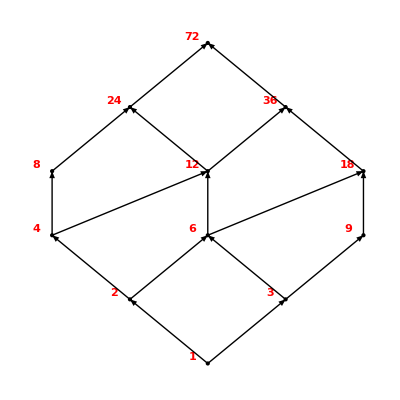

```mathematica
A=Deje2;
R=Reje2;
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

```mathematica
MINIMO[A_,R_]:=Module[{minimo,mini,n,m},minimo={};Do[mini=True;
Do[
If[MemberQ[R,{A[[n]],A[[m]]}],,mini=False;Break[];],{m,1,Length[A]}];
If[mini,AppendTo[minimo,A[[n]]];Break[];];,{n,1,Length[A]}];minimo];
```

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales]
```

```mathematica
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales];
```

```mathematica
MAXIMO[A_,R_]:=Module[{maximo,maxi,n,m},maximo={};
Do[maxi=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}],,maxi=False;Break[];],{m,1,Length[A]}];
If[maxi,AppendTo[maximo,A[[n]]];Break[];];,{n,1,Length[A]}];
maximo]
```

```mathematica
A={};

For[i=1,i<=Length[Deje2],i++,
If[Deje2[[i]]>6&&EvenQ[Deje2[[i]]],
AppendTo[A,Deje2[[i]]]
]
]

A
```

{8,12,18,24,36,72}

```mathematica
MINIMALES[A,R]
MINIMO[A,R]
MAXIMALES[A,R]
MAXIMO[A,R]
```

{8,12,18}

{}

{72}

{}

## Ejercicio 3

```mathematica
RETICULO[A_,R_]:=Module[{reticulo,cotassuperiores,cotasinferiores,csuper,cinfer,supremo,infimo,mini,maxi,n,m,x1,x2},reticulo=True;
Do[Do[cotassuperiores={};cotasinferiores={};
Do[csuper=True;cinfer=True;
If[Intersection[{{A[[x1]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[x2]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[n]],A[[x1]]}},R]=={},cinfer=False];
If[Intersection[{{A[[n]],A[[x2]]}},R]=={},cinfer=False];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};infimo={};
Do[mini=True;
Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];
If[supremo=={},reticulo=False];
Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];
         ,{n,1,Length[cotasinferiores]}];
If[infimo=={},reticulo=False];
      ,{x1,1,Length[A]}];
   ,{x2,1,Length[A]}];
reticulo
]
```

```mathematica
RETICULO[Deje2,Reje2]
```

True

Es un retículo

```mathematica
SubsetQ[Deje2,A]
```

True

Como D es un retículo y A es un subconjunto no vacío de D entonces es un subretículo de D

```mathematica
INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,n,m},
cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
infimo={};
Do[maxi=True;
Do[If[MemberQ[R,{cotasinferiores[[m]],cotasinferiores[[n]]}],,maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,{n,1,Length[cotasinferiores]}];
infimo
]
```

```mathematica
RETICULODISTRIBUTIVO[A_,R_]:=Module[{distributive,i,j,k},distributivo=True;
Do[Do[Do[If[TrueQ[SUPREMO[A,Union[{A[[i]]},INFIMO[A,{A[[j]],A[[k]]},R]],R]==INFIMO[A,Union[SUPREMO[A,{A[[i]],A[[j]]},R],SUPREMO[A,{A[[i]],A[[k]]},R]],R]],,distributivo=False;];         
,{i,1,Length[A]}];
      ,{j,1,Length[A]}];
   ,{k,1,Length[A]}];
distributivo
]
```

```mathematica
COMPLEMENTADO[A_,R_]:=Module[{complementado,k},complementado=True;
Do[If[COMPLEMENTO[A,R,A[[k]]]=={},complementado=False],{k,1,Length[A]}];
complementado]
```

```mathematica
COMPLEMENTO[A_,R_,n_]:=Module[{complemento,k},complemento={};
Do[If[INFIMO[A,{A[[k]],n},R]==MINIMALES[A,R]&&SUPREMO[A,{A[[k]],n},R]==MAXIMALES[A,R],AppendTo[complemento,A[[k]]]],{k,1,Length[A]}];
complemento]
```

```mathematica
MAXIMALES[Deje2,Reje2]
```

{72}

```mathematica
MINIMALES[Deje2,Reje2]
```

{1}

```mathematica
COMPLEMENTADO[Deje2,Reje2]
```

False

```mathematica
RETICULODISTRIBUTIVO[Deje2,Reje2]
```

True

Es un alg de Boole, ya que es un retículo distributivo y es un retículo con elemento 0 y 1, y no es complementado

## Ejercicio 4

```mathematica
Inverso2[x_,n_]:=Module[{Cocientes,Euclides,Resto,a1,a2},Euclides[n1_,n2_]:=If[Mod[n1,n2]==0,n2,AppendTo[Cocientes,Quotient[n1,n2]];
Euclides[n2,Mod[n1,n2]]];Resto[1,x1_,x2_]:=x1-x2*Cocientes[[1]];
Resto[2,x1_,x2_]:=x2-Resto[1,x1,x2]*Cocientes[[2]];
Resto[k_,x1_,x2_]:=Expand[Resto[k-2,x1,x2]-Resto[k-1,x1,x2]*Cocientes[[k]]];a1=Abs[x];a2=Abs[n];Cocientes={};Euclides[a1,a2];Return[Mod[Resto[Length[Cocientes],1,0]*Sign[x],n]];];
```

```mathematica
Inverso2[120,23]
```

14

```mathematica
Inverso2[5,9]
```

2

```mathematica
Inverso2[7,100]
```

43

```mathematica
Mod[43*3,7]
```

3

```mathematica
Inverso2[11,55]
```

1

```mathematica
AlgChino2[a_,m_]:=Module[{M,b,Teorema,n,u,w,x0},Teorema="sí";n=Length[a];
Do[Do[If[GCD[m[[i]],m[[j]]]≠1,Teorema="no";Break[];],{j,i+1,Length[m]}],{i,Length[m]-1}];
If[Teorema=="sí",Inverso[x_,n_]:=Module[{inverso},Do[If[Mod[j*x,n]==1,inverso=j;Break[]],{j,1,n-1}];
Return[inverso]];
M[1]=1;M[i_]:=M[i-1]*m[[i-1]];
u[i_]:=Inverso[M[i],m[[i]]];
b[1]=Mod[a[[1]],m[[1]]];
w[i_]:=Mod[(a[[i]]-b[i-1])*u[i],m[[i]]];
b[i_]:=b[i-1]+w[i] M[i];
x0=b[Length[a]];
Print["Solución: x = ",x0," + t*",M[n+1]];
Print[TableForm[Join[{{a[[1]],m[[1]],1,1,"-",b[1]}},Table[{a[[i]],m[[i]],M[i],u[i],w[i],b[i]},{i,2,n}]],TableHeadings->{Table[i,{i,n}],{"a","m","M","u","w","b"}}]];,Print["No podemos aplicar el T.aa Chino del Resto"];];];
```

```mathematica
AlgChino2[{4,3,4},{5,7,11}]
```

Solución: x = 59 + t*385

| a | m | M | u | w | b
1 | 4 | 5 | 1 | 1 | - | 4
2 | 3 | 7 | 5 | 3 | 4 | 24
3 | 4 | 11 | 35 | 6 | 1 | 59